```mathematica
SetDirectory[NotebookDirectory[]];
```

## p10q3

```mathematica
cstn[x_]:=ToExpression[StringDelete[StringReplace[x,{"e+"->"*10^","e-"->"*10^-","j"->"I"}],{"(",")"}]];
gapedgefind[d_]:=Min[Abs[d]]-10^(-6);
leftfind[d_]:=(Transpose@Position[d,_?(#<0&)])[[1]];
rightfind[d_]:=(Transpose@Position[d,_?(#>0&)])[[1]];
```

```mathematica
datadir="../Processed_Data/1_DOS_GapFunctionAlpha_AFM";
```

```mathematica
a0b1v0d8data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a0_amag1_U0.8_eigvals.txt"],"Data"])[[1]]]];
a0d2b1v0d8data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a0.2_amag1_U0.8_eigvals.txt"],"Data"])[[1]]]];
a0d4b1v0d8data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a0.4_amag1_U0.8_eigvals.txt"],"Data"])[[1]]]];
a0d5b1v0d8data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a0.5_amag1_U0.8_eigvals.txt"],"Data"])[[1]]]];
a0d6b1v0d8data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a0.6_amag1_U0.8_eigvals.txt"],"Data"])[[1]]]];
```

```mathematica
linethickness=0.006;
```

```mathematica
xrange={-3,3};
yrange={0,0.8};
```

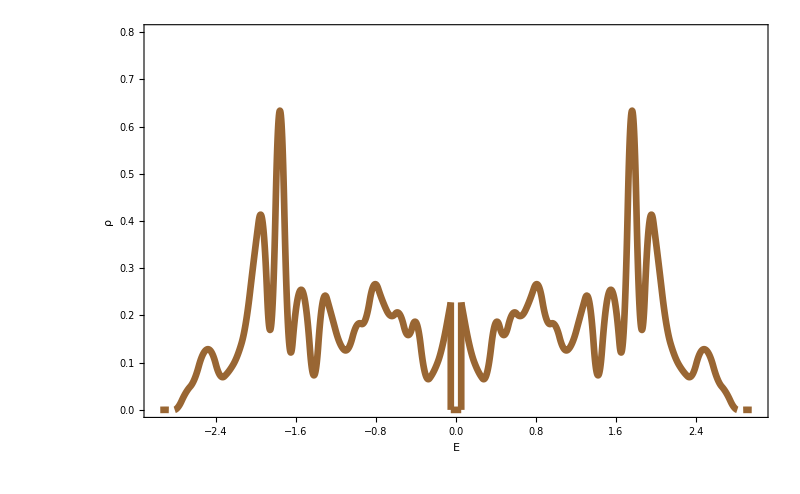

```mathematica
linecolor=Brown;
datasize=Length[a0b1v0d8data]; (**)

gapedge=gapedgefind[a0b1v0d8data]; (**)
leftdata=a0b1v0d8data[[leftfind[a0b1v0d8data]]];(**)
rightdata=a0b1v0d8data[[rightfind[a0b1v0d8data]]];(**)

numbergappoints=50;
numberbins=71;
bw=(3-gapedge)/((numberbins-1)/2);
leftbinedges=Subdivide[-3,-gapedge,(numberbins-1)/2];
rightbinedges=Subdivide[gapedge,3,(numberbins-1)/2];
leftbincenters=(leftbinedges+0.5*bw)[[;;-2]];
rightbincenters=(rightbinedges+0.5*bw)[[;;-2]];
gapbincenters=Subdivide[leftbincenters[[-1]],rightbincenters[[1]],numbergappoints-1];

leftcounts=BinCounts[leftdata,{leftbinedges}]/datasize/bw;
rightcounts=BinCounts[rightdata,{rightbinedges}]/datasize/bw;
gapcounts=ConstantArray[0,numbergappoints];

bincenters=Join[leftbincenters,gapbincenters,rightbincenters];
counts=Join[leftcounts,gapcounts,rightcounts];

a0b1v0d8hist=Show[
ListPlot[Transpose@{leftbincenters,leftcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{rightbincenters,rightcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{gapbincenters,gapcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{leftbincenters[[-1]],gapbincenters[[1]]},{leftcounts[[-1]],gapcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{gapbincenters[[-1]],rightbincenters[[1]]},{gapcounts[[-1]],rightcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"StyleBox[\"E\",FontSize->36]","StyleBox[\"ρ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

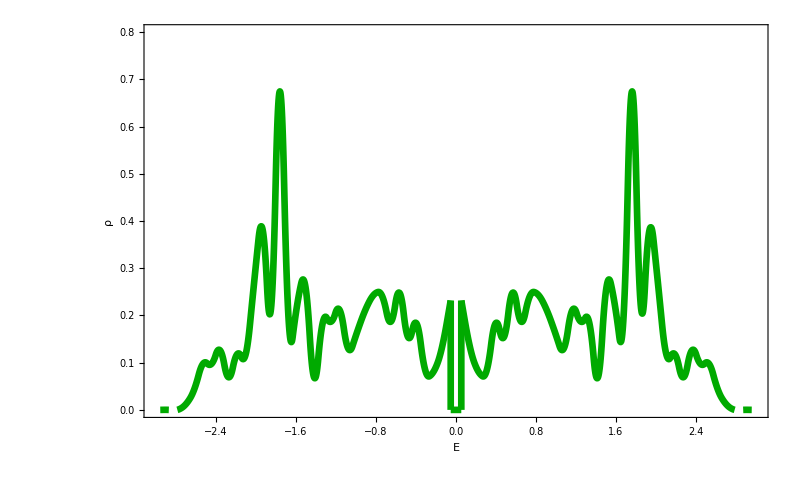

```mathematica
linecolor=Darker[Green];
datasize=Length[a0d2b1v0d8data]; (**)

gapedge=gapedgefind[a0d2b1v0d8data]; (**)
leftdata=a0d2b1v0d8data[[leftfind[a0d2b1v0d8data]]];(**)
rightdata=a0d2b1v0d8data[[rightfind[a0d2b1v0d8data]]];(**)

numbergappoints=50;
numberbins=71;
bw=(3-gapedge)/((numberbins-1)/2);
leftbinedges=Subdivide[-3,-gapedge,(numberbins-1)/2];
rightbinedges=Subdivide[gapedge,3,(numberbins-1)/2];
leftbincenters=(leftbinedges+0.5*bw)[[;;-2]];
rightbincenters=(rightbinedges+0.5*bw)[[;;-2]];
gapbincenters=Subdivide[leftbincenters[[-1]],rightbincenters[[1]],numbergappoints-1];

leftcounts=BinCounts[leftdata,{leftbinedges}]/datasize/bw;
rightcounts=BinCounts[rightdata,{rightbinedges}]/datasize/bw;
gapcounts=ConstantArray[0,numbergappoints];

bincenters=Join[leftbincenters,gapbincenters,rightbincenters];
counts=Join[leftcounts,gapcounts,rightcounts];

a0d2b1v0d8hist=Show[
ListPlot[Transpose@{leftbincenters,leftcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{rightbincenters,rightcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{gapbincenters,gapcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{leftbincenters[[-1]],gapbincenters[[1]]},{leftcounts[[-1]],gapcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{gapbincenters[[-1]],rightbincenters[[1]]},{gapcounts[[-1]],rightcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"StyleBox[\"E\",FontSize->36]","StyleBox[\"ρ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

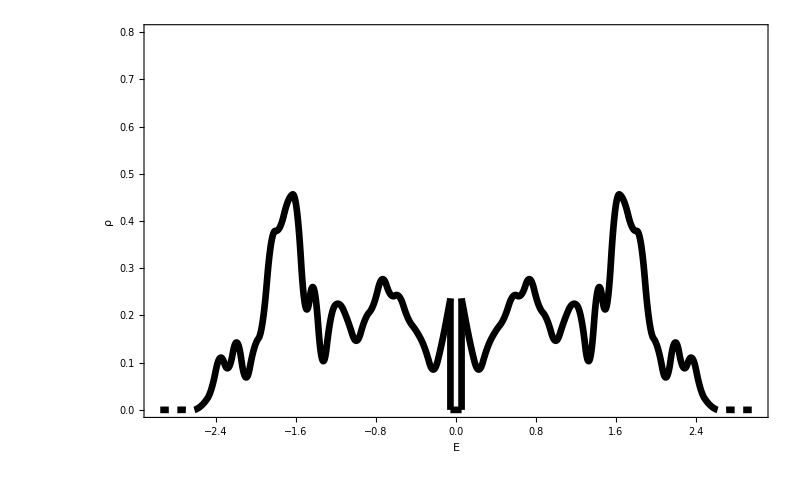

```mathematica
linecolor=Black;
datasize=Length[a0d4b1v0d8data]; (**)

gapedge=gapedgefind[a0d4b1v0d8data]; (**)
leftdata=a0d4b1v0d8data[[leftfind[a0d4b1v0d8data]]];(**)
rightdata=a0d4b1v0d8data[[rightfind[a0d4b1v0d8data]]];(**)

numbergappoints=50;
numberbins=71;
bw=(3-gapedge)/((numberbins-1)/2);
leftbinedges=Subdivide[-3,-gapedge,(numberbins-1)/2];
rightbinedges=Subdivide[gapedge,3,(numberbins-1)/2];
leftbincenters=(leftbinedges+0.5*bw)[[;;-2]];
rightbincenters=(rightbinedges+0.5*bw)[[;;-2]];
gapbincenters=Subdivide[leftbincenters[[-1]],rightbincenters[[1]],numbergappoints-1];

leftcounts=BinCounts[leftdata,{leftbinedges}]/datasize/bw;
rightcounts=BinCounts[rightdata,{rightbinedges}]/datasize/bw;
gapcounts=ConstantArray[0,numbergappoints];

bincenters=Join[leftbincenters,gapbincenters,rightbincenters];
counts=Join[leftcounts,gapcounts,rightcounts];

a0d4b1v0d8hist=Show[
ListPlot[Transpose@{leftbincenters,leftcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{rightbincenters,rightcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{gapbincenters,gapcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{leftbincenters[[-1]],gapbincenters[[1]]},{leftcounts[[-1]],gapcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{gapbincenters[[-1]],rightbincenters[[1]]},{gapcounts[[-1]],rightcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"StyleBox[\"E\",FontSize->36]","StyleBox[\"ρ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

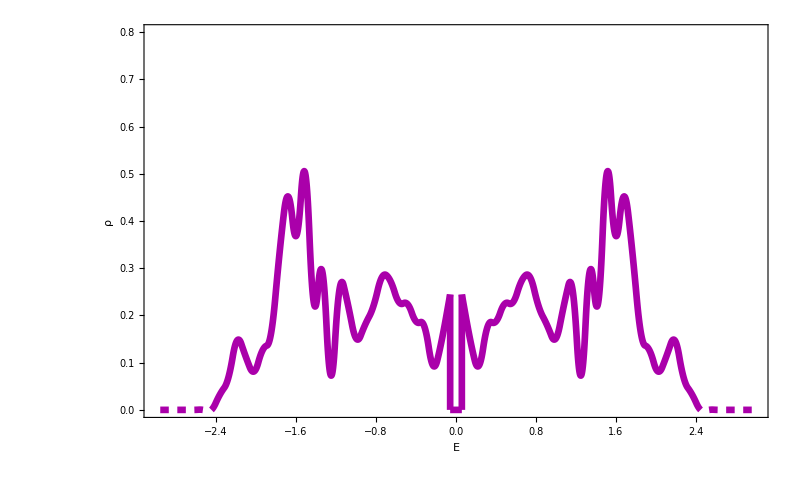

```mathematica
linecolor=Darker[Magenta];
datasize=Length[a0d5b1v0d8data]; (**)

gapedge=gapedgefind[a0d5b1v0d8data]; (**)
leftdata=a0d5b1v0d8data[[leftfind[a0d5b1v0d8data]]];(**)
rightdata=a0d5b1v0d8data[[rightfind[a0d5b1v0d8data]]];(**)

numbergappoints=50;
numberbins=71;
bw=(3-gapedge)/((numberbins-1)/2);
leftbinedges=Subdivide[-3,-gapedge,(numberbins-1)/2];
rightbinedges=Subdivide[gapedge,3,(numberbins-1)/2];
leftbincenters=(leftbinedges+0.5*bw)[[;;-2]];
rightbincenters=(rightbinedges+0.5*bw)[[;;-2]];
gapbincenters=Subdivide[leftbincenters[[-1]],rightbincenters[[1]],numbergappoints-1];

leftcounts=BinCounts[leftdata,{leftbinedges}]/datasize/bw;
rightcounts=BinCounts[rightdata,{rightbinedges}]/datasize/bw;
gapcounts=ConstantArray[0,numbergappoints];

bincenters=Join[leftbincenters,gapbincenters,rightbincenters];
counts=Join[leftcounts,gapcounts,rightcounts];

a0d5b1v0d8hist=Show[
ListPlot[Transpose@{leftbincenters,leftcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{rightbincenters,rightcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{gapbincenters,gapcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{leftbincenters[[-1]],gapbincenters[[1]]},{leftcounts[[-1]],gapcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{gapbincenters[[-1]],rightbincenters[[1]]},{gapcounts[[-1]],rightcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"StyleBox[\"E\",FontSize->36]","StyleBox[\"ρ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

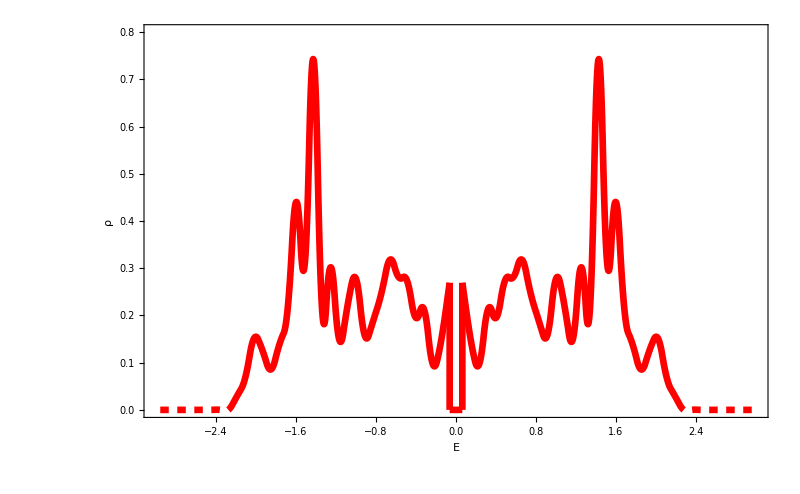

```mathematica
linecolor=Red;
datasize=Length[a0d6b1v0d8data]; (**)

gapedge=gapedgefind[a0d6b1v0d8data]; (**)
leftdata=a0d6b1v0d8data[[leftfind[a0d6b1v0d8data]]];(**)
rightdata=a0d6b1v0d8data[[rightfind[a0d6b1v0d8data]]];(**)

numbergappoints=50;
numberbins=71;
bw=(3-gapedge)/((numberbins-1)/2);
leftbinedges=Subdivide[-3,-gapedge,(numberbins-1)/2];
rightbinedges=Subdivide[gapedge,3,(numberbins-1)/2];
leftbincenters=(leftbinedges+0.5*bw)[[;;-2]];
rightbincenters=(rightbinedges+0.5*bw)[[;;-2]];
gapbincenters=Subdivide[leftbincenters[[-1]],rightbincenters[[1]],numbergappoints-1];

leftcounts=BinCounts[leftdata,{leftbinedges}]/datasize/bw;
rightcounts=BinCounts[rightdata,{rightbinedges}]/datasize/bw;
gapcounts=ConstantArray[0,numbergappoints];

bincenters=Join[leftbincenters,gapbincenters,rightbincenters];
counts=Join[leftcounts,gapcounts,rightcounts];

a0d6b1v0d8hist=Show[
ListPlot[Transpose@{leftbincenters,leftcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{rightbincenters,rightcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{gapbincenters,gapcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{leftbincenters[[-1]],gapbincenters[[1]]},{leftcounts[[-1]],gapcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{gapbincenters[[-1]],rightbincenters[[1]]},{gapcounts[[-1]],rightcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"StyleBox[\"E\",FontSize->36]","StyleBox[\"ρ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

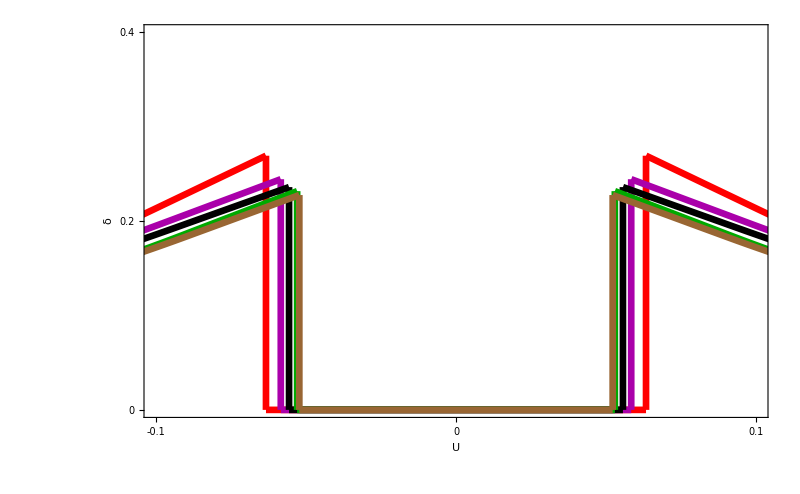

```mathematica
Show[
a0d6b1v0d8hist,a0d5b1v0d8hist,a0d4b1v0d8hist,a0d2b1v0d8hist,a0b1v0d8hist,

PlotRange->{{-0.1,0.1},{0,0.4}},
BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"U","δ"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.2,0.4},None},{{-0.1,0,0.1},None}},FrameTicksStyle->FontSize->50
]
```

## p14q3

```mathematica
cstn[x_]:=ToExpression[StringDelete[StringReplace[x,{"e+"->"*10^","e-"->"*10^-","j"->"I"}],{"(",")"}]];
gapedgefind[d_]:=Min[Abs[d]]-10^(-6);
leftfind[d_]:=(Transpose@Position[d,_?(#<0&)])[[1]];
rightfind[d_]:=(Transpose@Position[d,_?(#>0&)])[[1]];
```

```mathematica
datadir="../Processed_Data/1_DOS_GapFunctionAlpha_AFM";
```

```mathematica
a0b1v0d7data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a0_amag1_U0.7_eigvals.txt"],"Data"])[[1]]]];
a0d2b1v0d7data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a0.2_amag1_U0.7_eigvals.txt"],"Data"])[[1]]]];
a0d4b1v0d7data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a0.4_amag1_U0.7_eigvals.txt"],"Data"])[[1]]]];
a0d6b1v0d7data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a0.6_amag1_U0.7_eigvals.txt"],"Data"])[[1]]]];
a0d7b1v0d7data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a0.7_amag1_U0.7_eigvals.txt"],"Data"])[[1]]]];
```

```mathematica
linethickness=0.006;
```

```mathematica
xrange={-3,3};
yrange={0,0.8};
```

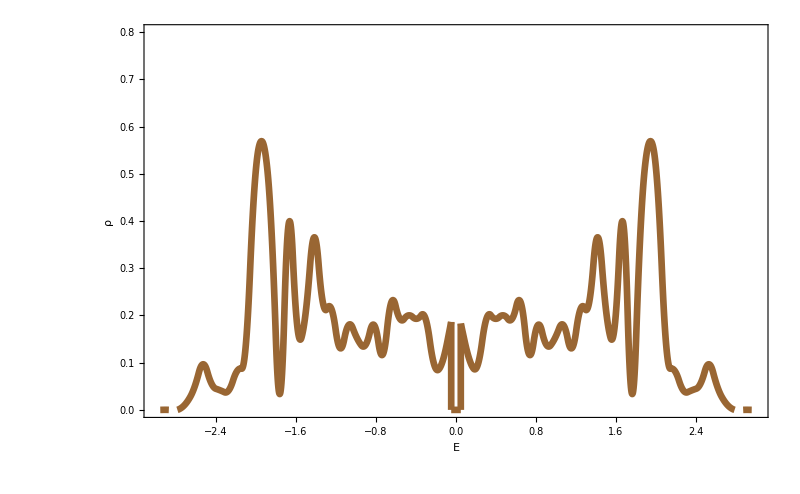

```mathematica
linecolor=Brown;
datasize=Length[a0b1v0d7data]; (**)

gapedge=gapedgefind[a0b1v0d7data]; (**)
leftdata=a0b1v0d7data[[leftfind[a0b1v0d7data]]];(**)
rightdata=a0b1v0d7data[[rightfind[a0b1v0d7data]]];(**)

numbergappoints=50;
numberbins=71;
bw=(3-gapedge)/((numberbins-1)/2);
leftbinedges=Subdivide[-3,-gapedge,(numberbins-1)/2];
rightbinedges=Subdivide[gapedge,3,(numberbins-1)/2];
leftbincenters=(leftbinedges+0.5*bw)[[;;-2]];
rightbincenters=(rightbinedges+0.5*bw)[[;;-2]];
gapbincenters=Subdivide[leftbincenters[[-1]],rightbincenters[[1]],numbergappoints-1];

leftcounts=BinCounts[leftdata,{leftbinedges}]/datasize/bw;
rightcounts=BinCounts[rightdata,{rightbinedges}]/datasize/bw;
gapcounts=ConstantArray[0,numbergappoints];

bincenters=Join[leftbincenters,gapbincenters,rightbincenters];
counts=Join[leftcounts,gapcounts,rightcounts];

a0b1v0d7hist=Show[
ListPlot[Transpose@{leftbincenters,leftcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{rightbincenters,rightcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{gapbincenters,gapcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{leftbincenters[[-1]],gapbincenters[[1]]},{leftcounts[[-1]],gapcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{gapbincenters[[-1]],rightbincenters[[1]]},{gapcounts[[-1]],rightcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"StyleBox[\"E\",FontSize->36]","StyleBox[\"ρ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

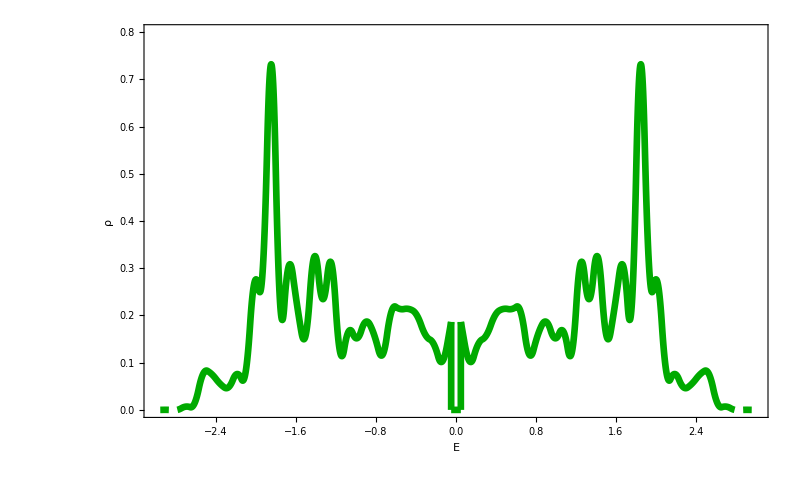

```mathematica
linecolor=Darker[Green];
datasize=Length[a0d2b1v0d7data]; (**)

gapedge=gapedgefind[a0d2b1v0d7data]; (**)
leftdata=a0d2b1v0d7data[[leftfind[a0d2b1v0d7data]]];(**)
rightdata=a0d2b1v0d7data[[rightfind[a0d2b1v0d7data]]];(**)

numbergappoints=50;
numberbins=71;
bw=(3-gapedge)/((numberbins-1)/2);
leftbinedges=Subdivide[-3,-gapedge,(numberbins-1)/2];
rightbinedges=Subdivide[gapedge,3,(numberbins-1)/2];
leftbincenters=(leftbinedges+0.5*bw)[[;;-2]];
rightbincenters=(rightbinedges+0.5*bw)[[;;-2]];
gapbincenters=Subdivide[leftbincenters[[-1]],rightbincenters[[1]],numbergappoints-1];

leftcounts=BinCounts[leftdata,{leftbinedges}]/datasize/bw;
rightcounts=BinCounts[rightdata,{rightbinedges}]/datasize/bw;
gapcounts=ConstantArray[0,numbergappoints];

bincenters=Join[leftbincenters,gapbincenters,rightbincenters];
counts=Join[leftcounts,gapcounts,rightcounts];

a0d2b1v0d7hist=Show[
ListPlot[Transpose@{leftbincenters,leftcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{rightbincenters,rightcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{gapbincenters,gapcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{leftbincenters[[-1]],gapbincenters[[1]]},{leftcounts[[-1]],gapcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{gapbincenters[[-1]],rightbincenters[[1]]},{gapcounts[[-1]],rightcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"StyleBox[\"E\",FontSize->36]","StyleBox[\"ρ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

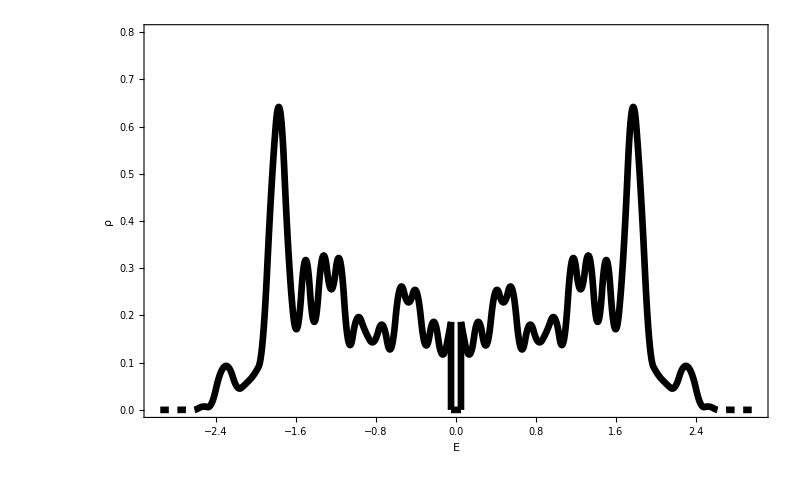

```mathematica
linecolor=Black;
datasize=Length[a0d4b1v0d7data]; (**)

gapedge=gapedgefind[a0d4b1v0d7data]; (**)
leftdata=a0d4b1v0d7data[[leftfind[a0d4b1v0d7data]]];(**)
rightdata=a0d4b1v0d7data[[rightfind[a0d4b1v0d7data]]];(**)

numbergappoints=50;
numberbins=71;
bw=(3-gapedge)/((numberbins-1)/2);
leftbinedges=Subdivide[-3,-gapedge,(numberbins-1)/2];
rightbinedges=Subdivide[gapedge,3,(numberbins-1)/2];
leftbincenters=(leftbinedges+0.5*bw)[[;;-2]];
rightbincenters=(rightbinedges+0.5*bw)[[;;-2]];
gapbincenters=Subdivide[leftbincenters[[-1]],rightbincenters[[1]],numbergappoints-1];

leftcounts=BinCounts[leftdata,{leftbinedges}]/datasize/bw;
rightcounts=BinCounts[rightdata,{rightbinedges}]/datasize/bw;
gapcounts=ConstantArray[0,numbergappoints];

bincenters=Join[leftbincenters,gapbincenters,rightbincenters];
counts=Join[leftcounts,gapcounts,rightcounts];

a0d4b1v0d7hist=Show[
ListPlot[Transpose@{leftbincenters,leftcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{rightbincenters,rightcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{gapbincenters,gapcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{leftbincenters[[-1]],gapbincenters[[1]]},{leftcounts[[-1]],gapcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{gapbincenters[[-1]],rightbincenters[[1]]},{gapcounts[[-1]],rightcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"StyleBox[\"E\",FontSize->36]","StyleBox[\"ρ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

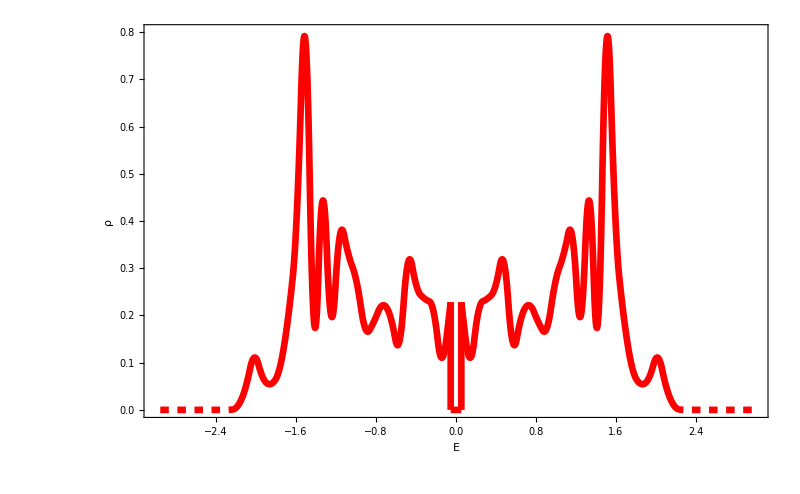

```mathematica
linecolor=Red;
datasize=Length[a0d6b1v0d7data]; (**)

gapedge=gapedgefind[a0d6b1v0d7data]; (**)
leftdata=a0d6b1v0d7data[[leftfind[a0d6b1v0d7data]]];(**)
rightdata=a0d6b1v0d7data[[rightfind[a0d6b1v0d7data]]];(**)

numbergappoints=50;
numberbins=71;
bw=(3-gapedge)/((numberbins-1)/2);
leftbinedges=Subdivide[-3,-gapedge,(numberbins-1)/2];
rightbinedges=Subdivide[gapedge,3,(numberbins-1)/2];
leftbincenters=(leftbinedges+0.5*bw)[[;;-2]];
rightbincenters=(rightbinedges+0.5*bw)[[;;-2]];
gapbincenters=Subdivide[leftbincenters[[-1]],rightbincenters[[1]],numbergappoints-1];

leftcounts=BinCounts[leftdata,{leftbinedges}]/datasize/bw;
rightcounts=BinCounts[rightdata,{rightbinedges}]/datasize/bw;
gapcounts=ConstantArray[0,numbergappoints];

bincenters=Join[leftbincenters,gapbincenters,rightbincenters];
counts=Join[leftcounts,gapcounts,rightcounts];

a0d6b1v0d7hist=Show[
ListPlot[Transpose@{leftbincenters,leftcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{rightbincenters,rightcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{gapbincenters,gapcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{leftbincenters[[-1]],gapbincenters[[1]]},{leftcounts[[-1]],gapcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{gapbincenters[[-1]],rightbincenters[[1]]},{gapcounts[[-1]],rightcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"StyleBox[\"E\",FontSize->36]","StyleBox[\"ρ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

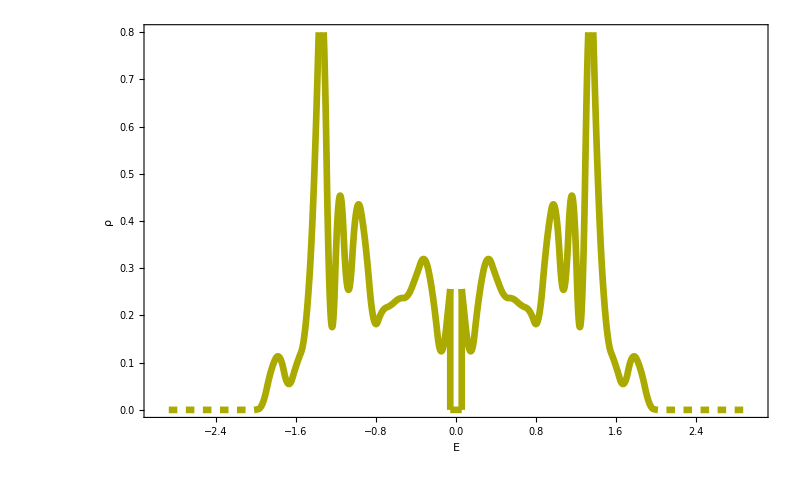

```mathematica
linecolor=Darker[Yellow];
datasize=Length[a0d7b1v0d7data]; (**)

gapedge=gapedgefind[a0d7b1v0d7data]; (**)
leftdata=a0d7b1v0d7data[[leftfind[a0d7b1v0d7data]]];(**)
rightdata=a0d7b1v0d7data[[rightfind[a0d7b1v0d7data]]];(**)

numbergappoints=50;
numberbins=71;
bw=(3-gapedge)/((numberbins-1)/2);
leftbinedges=Subdivide[-3,-gapedge,(numberbins-1)/2];
rightbinedges=Subdivide[gapedge,3,(numberbins-1)/2];
leftbincenters=(leftbinedges+0.5*bw)[[;;-2]];
rightbincenters=(rightbinedges+0.5*bw)[[;;-2]];
gapbincenters=Subdivide[leftbincenters[[-1]],rightbincenters[[1]],numbergappoints-1];

leftcounts=BinCounts[leftdata,{leftbinedges}]/datasize/bw;
rightcounts=BinCounts[rightdata,{rightbinedges}]/datasize/bw;
gapcounts=ConstantArray[0,numbergappoints];

bincenters=Join[leftbincenters,gapbincenters,rightbincenters];
counts=Join[leftcounts,gapcounts,rightcounts];

a0d7b1v0d7hist=Show[
ListPlot[Transpose@{leftbincenters,leftcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{rightbincenters,rightcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{gapbincenters,gapcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{leftbincenters[[-1]],gapbincenters[[1]]},{leftcounts[[-1]],gapcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{gapbincenters[[-1]],rightbincenters[[1]]},{gapcounts[[-1]],rightcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"StyleBox[\"E\",FontSize->36]","StyleBox[\"ρ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

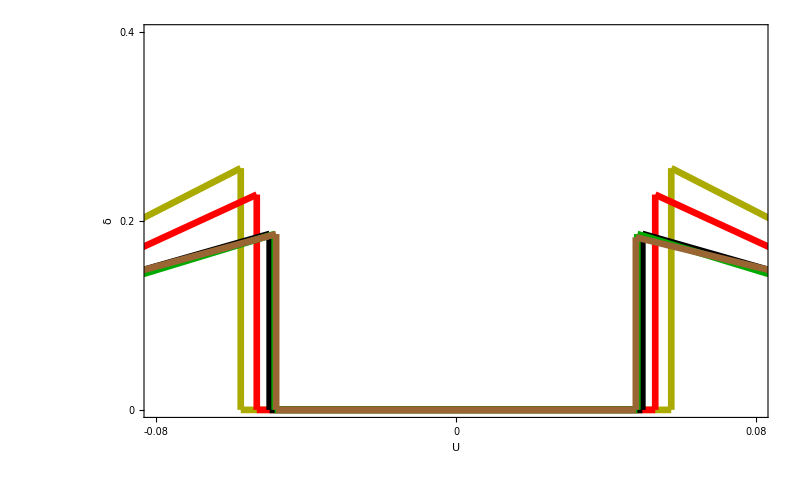

```mathematica
Show[
a0d7b1v0d7hist,a0d6b1v0d7hist,a0d4b1v0d7hist,a0d2b1v0d7hist,a0b1v0d7hist,

PlotRange->{{-0.08,0.08},{0,0.4}},
BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"U","δ"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.2,0.4},None},{{-0.08,0,0.08},None}},FrameTicksStyle->FontSize->50
]
```

## Honeycomb

```mathematica
cstn[x_]:=ToExpression[StringDelete[StringReplace[x,{"e+"->"*10^","e-"->"*10^-","j"->"I"}],{"(",")"}]];
gapedgefind[d_]:=Min[Abs[d]]-10^(-6);
leftfind[d_]:=(Transpose@Position[d,_?(#<0&)])[[1]];
rightfind[d_]:=(Transpose@Position[d,_?(#>0&)])[[1]];
```

```mathematica
datadir="../Processed_Data/1_DOS_GapFunctionAlpha_AFM";
```

```mathematica
a0b0d5v1data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a0_amag0.5_U1.0_eigvals.txt"],"Data"])[[1]]]];
a0d2b0d5v1data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a0.2_amag0.5_U1.0_eigvals.txt"],"Data"])[[1]]]];
a0d4b0d5v1data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a0.4_amag0.5_U1.0_eigvals.txt"],"Data"])[[1]]]];
a0d6b0d5v1data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a0.6_amag0.5_U1.0_eigvals.txt"],"Data"])[[1]]]];
a0d8b0d5v1data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a0.8_amag0.5_U1.0_eigvals.txt"],"Data"])[[1]]]];
```

```mathematica
linethickness=0.006;
```

```mathematica
xrange={-3,3};
yrange={0,0.8};
```

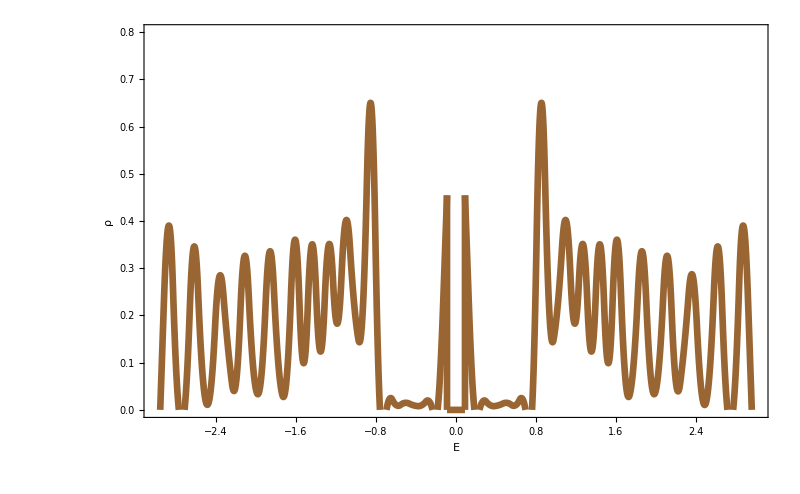

```mathematica
linecolor=Brown;
datasize=Length[a0b0d5v1data]; (**)

gapedge=gapedgefind[a0b0d5v1data]; (**)
leftdata=a0b0d5v1data[[leftfind[a0b0d5v1data]]];(**)
rightdata=a0b0d5v1data[[rightfind[a0b0d5v1data]]];(**)

numbergappoints=50;
numberbins=71;
bw=(3-gapedge)/((numberbins-1)/2);
leftbinedges=Subdivide[-3,-gapedge,(numberbins-1)/2];
rightbinedges=Subdivide[gapedge,3,(numberbins-1)/2];
leftbincenters=(leftbinedges+0.5*bw)[[;;-2]];
rightbincenters=(rightbinedges+0.5*bw)[[;;-2]];
gapbincenters=Subdivide[leftbincenters[[-1]],rightbincenters[[1]],numbergappoints-1];

leftcounts=BinCounts[leftdata,{leftbinedges}]/datasize/bw;
rightcounts=BinCounts[rightdata,{rightbinedges}]/datasize/bw;
gapcounts=ConstantArray[0,numbergappoints];

bincenters=Join[leftbincenters,gapbincenters,rightbincenters];
counts=Join[leftcounts,gapcounts,rightcounts];

a0b0d5v1hist=Show[
ListPlot[Transpose@{leftbincenters,leftcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{rightbincenters,rightcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{gapbincenters,gapcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{leftbincenters[[-1]],gapbincenters[[1]]},{leftcounts[[-1]],gapcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{gapbincenters[[-1]],rightbincenters[[1]]},{gapcounts[[-1]],rightcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"StyleBox[\"E\",FontSize->36]","StyleBox[\"ρ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

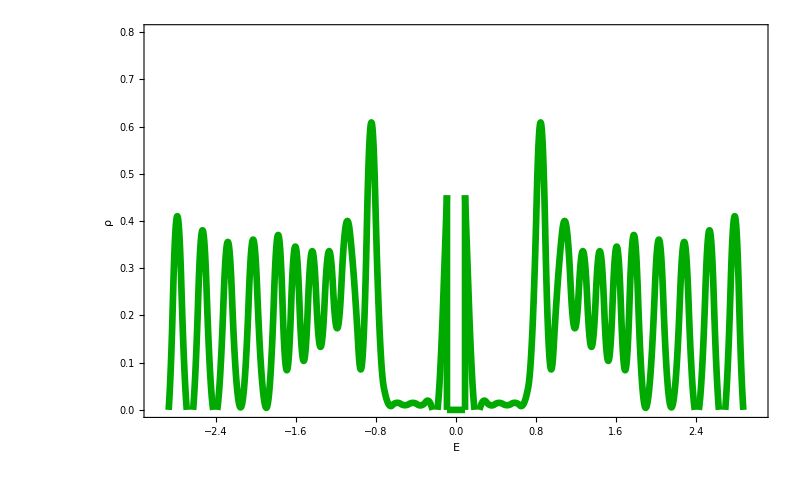

```mathematica
linecolor=Darker[Green];
datasize=Length[a0d2b0d5v1data]; (**)

gapedge=gapedgefind[a0d2b0d5v1data]; (**)
leftdata=a0d2b0d5v1data[[leftfind[a0d2b0d5v1data]]];(**)
rightdata=a0d2b0d5v1data[[rightfind[a0d2b0d5v1data]]];(**)

numbergappoints=50;
numberbins=71;
bw=(3-gapedge)/((numberbins-1)/2);
leftbinedges=Subdivide[-3,-gapedge,(numberbins-1)/2];
rightbinedges=Subdivide[gapedge,3,(numberbins-1)/2];
leftbincenters=(leftbinedges+0.5*bw)[[;;-2]];
rightbincenters=(rightbinedges+0.5*bw)[[;;-2]];
gapbincenters=Subdivide[leftbincenters[[-1]],rightbincenters[[1]],numbergappoints-1];

leftcounts=BinCounts[leftdata,{leftbinedges}]/datasize/bw;
rightcounts=BinCounts[rightdata,{rightbinedges}]/datasize/bw;
gapcounts=ConstantArray[0,numbergappoints];

bincenters=Join[leftbincenters,gapbincenters,rightbincenters];
counts=Join[leftcounts,gapcounts,rightcounts];

a0d2b0d5v1hist=Show[
ListPlot[Transpose@{leftbincenters,leftcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{rightbincenters,rightcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{gapbincenters,gapcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{leftbincenters[[-1]],gapbincenters[[1]]},{leftcounts[[-1]],gapcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{gapbincenters[[-1]],rightbincenters[[1]]},{gapcounts[[-1]],rightcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"StyleBox[\"E\",FontSize->36]","StyleBox[\"ρ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

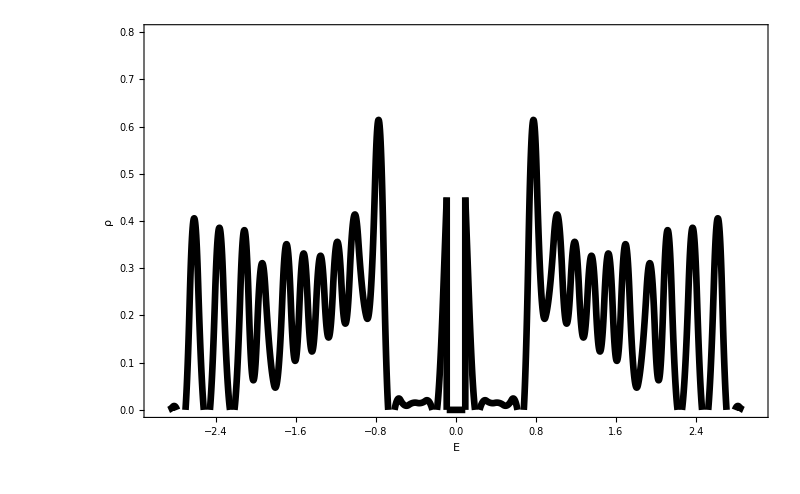

```mathematica
linecolor=Black;
datasize=Length[a0d4b0d5v1data]; (**)

gapedge=gapedgefind[a0d4b0d5v1data]; (**)
leftdata=a0d4b0d5v1data[[leftfind[a0d4b0d5v1data]]];(**)
rightdata=a0d4b0d5v1data[[rightfind[a0d4b0d5v1data]]];(**)

numbergappoints=50;
numberbins=71;
bw=(3-gapedge)/((numberbins-1)/2);
leftbinedges=Subdivide[-3,-gapedge,(numberbins-1)/2];
rightbinedges=Subdivide[gapedge,3,(numberbins-1)/2];
leftbincenters=(leftbinedges+0.5*bw)[[;;-2]];
rightbincenters=(rightbinedges+0.5*bw)[[;;-2]];
gapbincenters=Subdivide[leftbincenters[[-1]],rightbincenters[[1]],numbergappoints-1];

leftcounts=BinCounts[leftdata,{leftbinedges}]/datasize/bw;
rightcounts=BinCounts[rightdata,{rightbinedges}]/datasize/bw;
gapcounts=ConstantArray[0,numbergappoints];

bincenters=Join[leftbincenters,gapbincenters,rightbincenters];
counts=Join[leftcounts,gapcounts,rightcounts];

a0d4b0d5v1hist=Show[
ListPlot[Transpose@{leftbincenters,leftcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{rightbincenters,rightcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{gapbincenters,gapcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{leftbincenters[[-1]],gapbincenters[[1]]},{leftcounts[[-1]],gapcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{gapbincenters[[-1]],rightbincenters[[1]]},{gapcounts[[-1]],rightcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"StyleBox[\"E\",FontSize->36]","StyleBox[\"ρ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

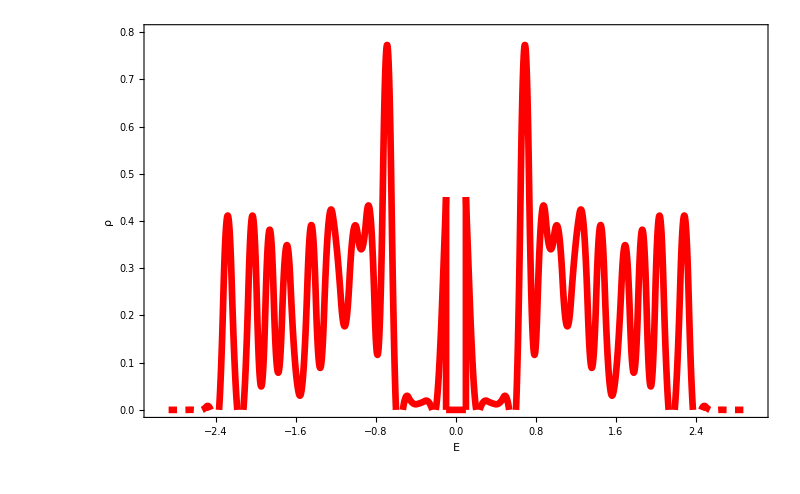

```mathematica
linecolor=Red;
datasize=Length[a0d6b0d5v1data]; (**)

gapedge=gapedgefind[a0d6b0d5v1data]; (**)
leftdata=a0d6b0d5v1data[[leftfind[a0d6b0d5v1data]]];(**)
rightdata=a0d6b0d5v1data[[rightfind[a0d6b0d5v1data]]];(**)

numbergappoints=50;
numberbins=71;
bw=(3-gapedge)/((numberbins-1)/2);
leftbinedges=Subdivide[-3,-gapedge,(numberbins-1)/2];
rightbinedges=Subdivide[gapedge,3,(numberbins-1)/2];
leftbincenters=(leftbinedges+0.5*bw)[[;;-2]];
rightbincenters=(rightbinedges+0.5*bw)[[;;-2]];
gapbincenters=Subdivide[leftbincenters[[-1]],rightbincenters[[1]],numbergappoints-1];

leftcounts=BinCounts[leftdata,{leftbinedges}]/datasize/bw;
rightcounts=BinCounts[rightdata,{rightbinedges}]/datasize/bw;
gapcounts=ConstantArray[0,numbergappoints];

bincenters=Join[leftbincenters,gapbincenters,rightbincenters];
counts=Join[leftcounts,gapcounts,rightcounts];

a0d6b0d5v1hist=Show[
ListPlot[Transpose@{leftbincenters,leftcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{rightbincenters,rightcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{gapbincenters,gapcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{leftbincenters[[-1]],gapbincenters[[1]]},{leftcounts[[-1]],gapcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{gapbincenters[[-1]],rightbincenters[[1]]},{gapcounts[[-1]],rightcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"StyleBox[\"E\",FontSize->36]","StyleBox[\"ρ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

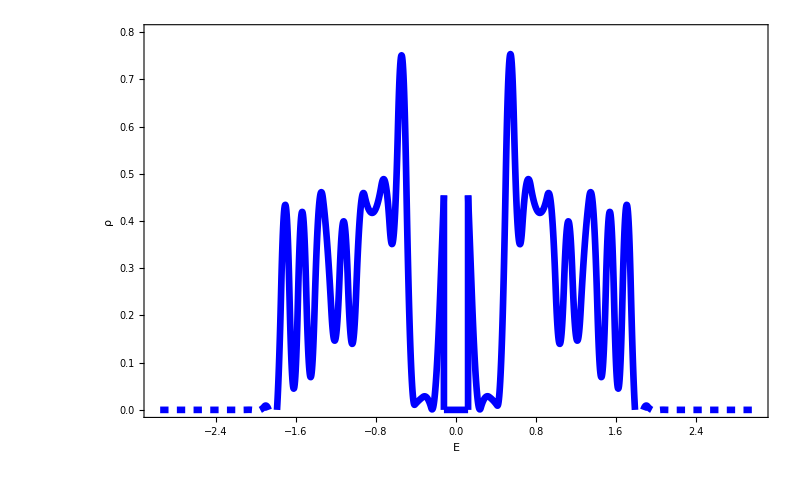

```mathematica
linecolor=Blue;
datasize=Length[a0d8b0d5v1data]; (**)

gapedge=gapedgefind[a0d8b0d5v1data]; (**)
leftdata=a0d8b0d5v1data[[leftfind[a0d8b0d5v1data]]];(**)
rightdata=a0d8b0d5v1data[[rightfind[a0d8b0d5v1data]]];(**)

numbergappoints=50;
numberbins=71;
bw=(3-gapedge)/((numberbins-1)/2);
leftbinedges=Subdivide[-3,-gapedge,(numberbins-1)/2];
rightbinedges=Subdivide[gapedge,3,(numberbins-1)/2];
leftbincenters=(leftbinedges+0.5*bw)[[;;-2]];
rightbincenters=(rightbinedges+0.5*bw)[[;;-2]];
gapbincenters=Subdivide[leftbincenters[[-1]],rightbincenters[[1]],numbergappoints-1];

leftcounts=BinCounts[leftdata,{leftbinedges}]/datasize/bw;
rightcounts=BinCounts[rightdata,{rightbinedges}]/datasize/bw;
gapcounts=ConstantArray[0,numbergappoints];

bincenters=Join[leftbincenters,gapbincenters,rightbincenters];
counts=Join[leftcounts,gapcounts,rightcounts];

a0d8b0d5v1hist=Show[
ListPlot[Transpose@{leftbincenters,leftcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{rightbincenters,rightcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{gapbincenters,gapcounts},Joined->True,InterpolationOrder->2,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{leftbincenters[[-1]],gapbincenters[[1]]},{leftcounts[[-1]],gapcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{gapbincenters[[-1]],rightbincenters[[1]]},{gapcounts[[-1]],rightcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{linecolor,Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"StyleBox[\"E\",FontSize->36]","StyleBox[\"ρ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

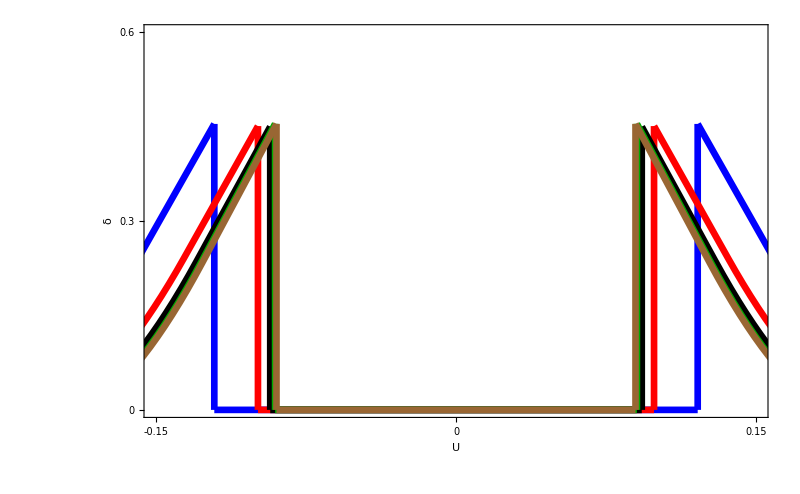

```mathematica
Show[
a0d8b0d5v1hist,a0d6b0d5v1hist,a0d4b0d5v1hist,a0d2b0d5v1hist,a0b0d5v1hist,

PlotRange->{{-0.15,0.15},{0,0.6}},
BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"U","δ"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.3,0.6},None},{{-0.15,0,0.15},None}},FrameTicksStyle->FontSize->50
]
```